## Comparing matchings

### Define Lagrangians, normalize canonically, FR and remove tadpole

```mathematica
LoadOperators[]:=Module[
{},

Clear[m2,λ,κ,g,T, ϵ];
maxOrder=8;

(*η=1 for effective operators and η=0 for NO effective operators*)

(* -------------------------------------------------------------------------------------------------------------------------------------------------------------------- *)
(* ----------------------------------------------------------------------Fermion and scalar loops---------------------------------------------------------------------- *)
(* -------------------------------------------------------------------------------------------------------------------------------------------------------------------- *)

(* Wilson coefficients and operators (BEFORE FIELD REDEFINITIONS) *)
(* After matching to the 4D theory at T>0,we find the following Wilson coefficients and operators in the 3dEFT Lagrangian: *)
(*O4*)
D2S2[r_]:=1/2 ϕ'[r]^2;
S1[r_]:=ϕ[r];
S2[r_]:=1/2 ϕ[r]^2;
S3[r_]:=ϕ[r]^3;
S4[r_]:=ϕ[r]^4;
opListO4={D2S2,S1,S2,S3, S4};

K = 1+g^2/(12 Pi^2)+(3 κ^2 Zeta[3])/(64 π^4 T^2);
σ3pre=1/4 T^(3/2) κ;
m32pre = m2 + g^2 T^2 / 6 + λ T^2;
κ3pre = Sqrt[T]κ;
λ3pre = T λ;
coeffListO4 = {K,σ3pre,m32pre, κ3pre, λ3pre};

(*O5*)
S5[r_]:=ϕ[r]^5;
D2S3[r_]:=ϕ[r]^2 (2 ϕ'[r] + r ϕ''[r])/r;
opListO5={S5,D2S3};

c51pre=(243 Zeta[7] κ^5)/(2048 π^8 T^(9/2))-(81 λ Zeta[5] κ^3)/(64 π^6 T^(5/2))+(27 λ^2 Zeta[3] κ)/(8 π^4 Sqrt[T]);
r51pre=(27 κ^3 Zeta[5])/(1024 π^6 T^(7/2))-(3 κ λ Zeta[3])/(32 π^4 T^(3/2));
coeffListO5={c51pre, ϵ^2*r51pre};

(*O6*)
S6[r_]:=ϕ[r]^6;
D4S2[r_]:=(2 ϕ'[r] + r ϕ''[r])^2/r^2;
D2S4[r_]:=ϕ[r]^3 (2 ϕ'[r] + r ϕ''[r])/r;
opListO6={S6,D4S2,D2S4}; (* Sign from change to Euclidean is included in coefficients *)

c61pre =-(7 Zeta[3] g^6)/(192 π^4)-(1701 κ^6 Zeta[9])/(16384 π^10 T^6)+(1215 κ^4 λ Zeta[7])/(1024 π^8 T^4)-(243 κ^2 λ^2 Zeta[5])/(64 π^6 T^2)+(9 λ^3 Zeta[3])/(4 π^4);
r61pre = -(7 Zeta[3] g^2)/(384 π^4 T^2)-(9 κ^2 Zeta[5])/(10240 π^6 T^4);
r62pre=(35 Zeta[3] g^4)/(576 π^4 T)-(135 κ^4 Zeta[7])/(4096 π^8 T^5)+(45 κ^2 λ Zeta[5])/(256 π^6 T^3)-(λ^2 Zeta[3])/(8 π^4 T);
coeffListO6 ={c61pre,ϵ^4 r61pre,ϵ^2 r62pre};

(*O7*)
S7[r_]:=ϕ[r]^7;
D2S5[r_]:=ϕ[r]^4 (2 ϕ'[r] + r ϕ''[r])/r;
D4S3A[r_]:=ϕ[r] (2 ϕ'[r] + r ϕ''[r])^2/r^2;
D4S3B[r_]:=ϕ'[r]^2 (2 ϕ'[r] + r ϕ''[r])/r;
opListO7={S7, D2S5, D4S3A, D4S3B};

c71pre=(6561 Zeta[11] κ^7)/(65536 π^12 T^(15/2))-(5103 λ Zeta[9] κ^5)/(4096 π^10 T^(11/2))+(1215 λ^2 Zeta[7] κ^3)/(256 π^8 T^(7/2))-(81 λ^3 Zeta[5] κ)/(16 π^6 T^(3/2));
r71pre=(2835 Zeta[9] κ^5)/(65536 π^10 T^(13/2))-(1215 λ Zeta[7] κ^3)/(4096 π^8 T^(9/2))+(27 λ^2 Zeta[5] κ)/(64 π^6 T^(5/2));
r72pre=-(9 κ λ Zeta[5])/(1280 π^6 T^(7/2))+(27 κ^3 Zeta[7])/(8192 π^8 T^(11/2));
r73pre=-(9 κ λ Zeta[5])/(1280 π^6 T^(7/2))+(9 κ^3 Zeta[7])/(4096 π^8 T^(11/2));
coeffListO7={c71pre, ϵ^2 r71pre, ϵ^4 r72pre, ϵ^4 r73pre};

(*O8*)
S8[r_]:=ϕ[r]^8;
D4S4A[r_]:=ϕ[r]^2(2 ϕ'[r]^2/r^2 +  ϕ''[r]^2);
D6S2[r_]:=(2 ϕ'[r] + r ϕ''[r])(4 ϕ'''[r] + r ϕ''''[r])/r ^2;
D4S4B[r_]:=ϕ[r]^3 (4 ϕ'''[r]+r ϕ''''[r])/r;
D4S4C[r_]:=-3 ϕ[r]^2 (2 ϕ'[r] + r ϕ''[r])^2/r^2;
D2S6[r_]:=ϕ[r]^5 (2 ϕ'[r] + r ϕ''[r])/r ;
opListO8={S8, D4S4A, D6S2, D4S4B, D4S4C, D2S6};(* Sign from change to Euclidean is included in coefficients *)

c81pre=(31 Zeta[5] g^8)/(2048 π^6 T)-(216513 κ^8 Zeta[13])/(2097152 π^14 T^9)+(45927 κ^6 λ Zeta[11])/(32768 π^12 T^7)-(25515 κ^4 λ^2 Zeta[9])/(4096 π^10 T^5)+(1215 κ^2 λ^3 Zeta[7])/(128 π^8 T^3)-(81 λ^4 Zeta[5])/(32 π^6 T);
c82pre = -(31 Zeta[5] g^4)/(10240 π^6 T^3)-(189 κ^4 Zeta[9])/(131072 π^10 T^7)+(9 κ^2 λ Zeta[7])/(1024 π^8 T^5)-(9 λ^2 Zeta[5])/(640 π^6 T^3);
r81pre = -(31 Zeta[5] g^2)/(10240 π^6 T^4)-(9 κ^2 Zeta[7])/(229376 π^8 T^6);
r82pre = (217 Zeta[5] g^4)/(20480 π^6 T^3)-(315 κ^4 Zeta[9])/(262144 π^10 T^7)+(9 κ^2 λ Zeta[7])/(2048 π^8 T^5)+(3 λ^2 Zeta[5])/(1280 π^6 T^3);
r83pre=(279 Zeta[5] g^4)/(20480 π^6 T^3)-(945 κ^4 Zeta[9])/(262144 π^10 T^7)+(45 κ^2 λ Zeta[7])/(4096 π^8 T^5)-(9 λ^2 Zeta[5])/(1280 π^6 T^3);
r84pre = -(217 Zeta[5] g^6)/(5120 π^6 T^2)-(15309 κ^6 Zeta[11])/(262144 π^12 T^8)+(3969 κ^4 λ Zeta[9])/(8192 π^10 T^6)-(1053 κ^2 λ^2 Zeta[7])/(1024 π^8 T^4)+(27 λ^3 Zeta[5])/(80 π^6 T^2);
coeffListO8={c81pre,ϵ^4 c82pre,ϵ^6 r81pre,ϵ^4 r82pre,ϵ^4 r83pre,ϵ^2 r84pre};

(* In order to normalize canonically,we divide each coefficient by a power of K^(1/2)equal to the number of ϕ’s and expand up to order 8 in g. In doing this,the coefficients that go with each operator will gain different orders of g,so the same operators will appear in different perturbative orders with different coefficients. *)
powerCounting={g->ϵ g,m2->ϵ^2 m2, κ->ϵ^2 κ, λ->ϵ^2 λ}; (* Actually m2/T^2 ~ g^2 ~ κ/T *)

coeffListpre=Flatten[{coeffListO4,coeffListO5, coeffListO6,coeffListO7,coeffListO8}]/.powerCounting;
opList=Table[Flatten[{opListO4,opListO5,opListO6,opListO7,opListO8}][[i]]@r,{i,Length[Flatten[{opListO4,opListO5,opListO6,opListO7,opListO8}]]}];
nFields=Exponent[Collect[opList/.{ϕ->(n ϕ[#]&)},n],n];
coeffList = {1,σ, m2, κ, λ, c51pre, r51pre, c61pre, r61pre, r62pre, c71pre, r71pre, r72pre, r73pre, c81pre, c82pre, r81pre, r82pre, r83pre, r84pre};
coeffListNorm=Normal[Series[Normal[Series[#,{g,0,maxOrder}]]&/@(Power[K^(-1/2)/.powerCounting,#1]#2&[nFields,coeffListpre]), {ϵ,0,maxOrder}]]; (* Added series in epsilon too to expand the kappa term in the kinetic term we divide by  *)

coeffListNormModFS=coeffListNorm/.ϵ->1;

(*-----Field redefinitions + shift to remove tadpole-----*)

(* Assign the new expressions to coeffs after canonical normalization *)
coeffListAux={1, σ3, m32, κ3, λ3, c51, r51, c61, r61, r62, c71, r71, r72, r73, c81, c82, r81, r82, r83, r84};
coeffListSubs =MapThread[Rule,{coeffListAux,coeffListNormModFS}];

(*σ3post= (-a (-m32-2r61 m32^2-2 m32^3 (4 r61^2+r81))+3/2 a^2 (2κ3+2m32 (r51+6r61κ3)+m32^2 (16r51r61+2r72-r73+84κ3 r61^2+18r81κ3))+a^5 (904/3 m32 r51^4+c61 (6+72m32r61)+1403/5 m32r62 r51^2+132/5 m32 r62^2+258/5 m32r51r71+6m32r84+270κ3 r51^3+153r51r62κ3+18r71κ3+4608r61 r51^2 κ3^2+702r61r62 κ3^2+648r51r72 κ3^2-207r51r73 κ3^2+81r82 κ3^2+54r83 κ3^2+c51 (r51 (30+696m32r61)-m32 (-60r72+21r73)+180r61κ3)+100λ3 r51^2+4008m32r61λ3 r51^2+24r62λ3+3072/5 m32r61r62λ3+2864/5 m32r51r72λ3-1014/5 m32r51r73λ3+336/5 m32r82λ3+48m32r83λ3+1704r51r61κ3λ3+144r72κ3λ3-42r73κ3λ3+4896λ3 r61^2 κ3^2+936r81λ3 κ3^2+96r61 λ3^2+10368/5 m32 r61^2 λ3^2+1824/5 m32r81 λ3^2)+7/30 a^6 (30c71+700c51 r51^2+150c51r62+5920κ3 r51^4+11640c51r51r61κ3+5124r62κ3 r51^2+441κ3 r62^2+864r51r71κ3+900c51r72κ3-240c51r73κ3+90r84κ3+180c61 (r51+6r61κ3)+2200λ3 r51^3+1200c51r61λ3+1140r51r62λ3+120r71λ3+72720r61κ3λ3 r51^2+10296r61r62κ3λ3+9432r51r72κ3λ3-2652r51r73κ3λ3+1188r82κ3λ3+720r83κ3λ3+6240r51r61 λ3^2+480r72 λ3^2-120r73 λ3^2+36864κ3 r61^2 λ3^2+6912r81κ3 λ3^2)+4/5 a^7 (10c81+70c71r51+310c61 r51^2+1100c51 r51^3+250r61 c51^2+60c61r62+525c51r51r62+50c51r71+3370λ3 r51^4+480c61r61λ3+5640c51r51r61λ3+2724r62λ3 r51^2+216λ3 r62^2+424r51r71λ3+400c51r72λ3-90c51r73λ3+40r84λ3+18880r61 r51^2 λ3^2+2496r61r62 λ3^2+2272r51r72 λ3^2-552r51r73 λ3^2+288r82 λ3^2+160r83 λ3^2+6144 r61^2 λ3^3+1152r81 λ3^3)-5/4 a^4 (c51 (-4-40m32r61)-4 (11κ3 r51^2+4r51 (24r61 κ3^2+λ3)+3κ3 (r62+3r72κ3-r73κ3+60 r61^2 κ3^2+12r81 κ3^2+8r61λ3))-m32 (48 r51^3+4r71+1664r61κ3 r51^2+276r61r62κ3+30r82κ3+24r83κ3+32r72λ3-12r73λ3+1824κ3λ3 r61^2+336r81κ3λ3+2r51 (15r62+130r72κ3-51r73κ3+168r61λ3)))+2/3 a^3 (6 (3r51κ3+9r61 κ3^2+λ3)+m32 (19 r51^2+6r62+336r51r61κ3+36r72κ3-15r73κ3+900 r61^2 κ3^2+180r81 κ3^2+48r61λ3)+m32^2 (330r61 r51^2+r51 (58r72-27r73)+6 (10r61r62+r82+r83+64λ3 r61^2+12r81λ3))));
m32post=2*(m32^3 (4 r61^2+r81)+3aκ3+6 a^2 (3r51κ3+9r61 κ3^2+λ3)+5/4 a^4 (12c61+540κ3 r51^3+306r51r62κ3+36r71κ3+9216r61 r51^2 κ3^2+1404r61r62 κ3^2+1296r51r72 κ3^2-414r51r73 κ3^2+162r82 κ3^2+108r83 κ3^2+60c51 (r51+6r61κ3)+200λ3 r51^2+48r62λ3+3408r51r61κ3λ3+288r72κ3λ3-84r73κ3λ3+9792λ3 r61^2 κ3^2+1872r81λ3 κ3^2+192r61 λ3^2)+7/10 a^5 (30c71+700c51 r51^2+150c51r62+5920κ3 r51^4+11640c51r51r61κ3+5124r62κ3 r51^2+441κ3 r62^2+864r51r71κ3+900c51r72κ3-240c51r73κ3+90r84κ3+180c61 (r51+6r61κ3)+2200λ3 r51^3+1200c51r61λ3+1140r51r62λ3+120r71λ3+72720r61κ3λ3 r51^2+10296r61r62κ3λ3+9432r51r72κ3λ3-2652r51r73κ3λ3+1188r82κ3λ3+720r83κ3λ3+6240r51r61 λ3^2+480r72 λ3^2-120r73 λ3^2+36864κ3 r61^2 λ3^2+6912r81κ3 λ3^2)+14/5 a^6 (10c81+70c71r51+310c61 r51^2+1100c51 r51^3+250r61 c51^2+60c61r62+525c51r51r62+50c51r71+3370λ3 r51^4+480c61r61λ3+5640c51r51r61λ3+2724r62λ3 r51^2+216λ3 r62^2+424r51r71λ3+400c51r72λ3-90c51r73λ3+40r84λ3+18880r61 r51^2 λ3^2+2496r61r62 λ3^2+2272r51r72 λ3^2-552r51r73 λ3^2+288r82 λ3^2+160r83 λ3^2+6144 r61^2 λ3^3+1152r81 λ3^3)+10 a^3 (c51+11κ3 r51^2+4r51 (24r61 κ3^2+λ3)+3κ3 (r62+3r72κ3-r73κ3+60 r61^2 κ3^2+12r81 κ3^2+8r61λ3))+1/2 m32^2 (2r61 (1+24ar51+30 a^2 (11 r51^2+2r62))+12a r61^2 (21κ3+64aλ3)+a (2r72 (3+58ar51)-3r73 (1+18ar51)+54r81κ3+12a (r82+r83+12r81λ3)))+1/6 m32 (3+18a (r51+6r61κ3)+6 a^2 (19 r51^2+6r62+336r51r61κ3+36r72κ3-15r73κ3+900 r61^2 κ3^2+180r81 κ3^2+48r61λ3)+15 a^3 (48 r51^3+40c51r61+4r71+1664r61κ3 r51^2+276r61r62κ3+30r82κ3+24r83κ3+32r72λ3-12r73λ3+1824κ3λ3 r61^2+336r81κ3λ3+2r51 (15r62+130r72κ3-51r73κ3+168r61λ3))+a^4 (4520 r51^4+r51^2 (4209r62+60120r61λ3)+6r51 (1740c51r61+129r71+λ3 (1432r72-507r73))+9 (120c61r61+44 r62^2+100c51r72-35c51r73+10r84+1024r61r62λ3+112r82λ3+80r83λ3+3456 r61^2 λ3^2+608r81 λ3^2))));
κ3post =(κ3+m32 (r51+6r61κ3)+m32^2 (8r51r61+r72-1/2 r73+42κ3 r61^2+9r81κ3)+a^3 (9040/9 m32 r51^4+c61 (20+240m32r61)+2806/3 m32r62 r51^2+88m32 r62^2+172m32r51r71+20m32r84+900κ3 r51^3+510r51r62κ3+60r71κ3+15360r61 r51^2 κ3^2+2340r61r62 κ3^2+2160r51r72 κ3^2-690r51r73 κ3^2+270r82 κ3^2+180r83 κ3^2-10c51 (2r51 (-5-116m32r61)-m32 (20r72-7r73)-60r61κ3)+1000/3 λ3 r51^2+13360m32r61λ3 r51^2+80r62λ3+2048m32r61r62λ3+5728/3 m32r51r72λ3-676m32r51r73λ3+224m32r82λ3+160m32r83λ3+5680r51r61κ3λ3+480r72κ3λ3-140r73κ3λ3+16320λ3 r61^2 κ3^2+3120r81λ3 κ3^2+320r61 λ3^2+6912m32 r61^2 λ3^2+1216m32r81 λ3^2)+7/6 a^4 (30c71+700c51 r51^2+150c51r62+5920κ3 r51^4+11640c51r51r61κ3+5124r62κ3 r51^2+441κ3 r62^2+864r51r71κ3+900c51r72κ3-240c51r73κ3+90r84κ3+180c61 (r51+6r61κ3)+2200λ3 r51^3+1200c51r61λ3+1140r51r62λ3+120r71λ3+72720r61κ3λ3 r51^2+10296r61r62κ3λ3+9432r51r72κ3λ3-2652r51r73κ3λ3+1188r82κ3λ3+720r83κ3λ3+6240r51r61 λ3^2+480r72 λ3^2-120r73 λ3^2+36864κ3 r61^2 λ3^2+6912r81κ3 λ3^2)+28/5 a^5 (10c81+70c71r51+310c61 r51^2+1100c51 r51^3+250r61 c51^2+60c61r62+525c51r51r62+50c51r71+3370λ3 r51^4+480c61r61λ3+5640c51r51r61λ3+2724r62λ3 r51^2+216λ3 r62^2+424r51r71λ3+400c51r72λ3-90c51r73λ3+40r84λ3+18880r61 r51^2 λ3^2+2496r61r62 λ3^2+2272r51r72 λ3^2-552r51r73 λ3^2+288r82 λ3^2+160r83 λ3^2+6144 r61^2 λ3^3+1152r81 λ3^3)-5/2 a^2 (c51 (-4-40m32r61)-4 (11κ3 r51^2+4r51 (24r61 κ3^2+λ3)+3κ3 (r62+3r72κ3-r73κ3+60 r61^2 κ3^2+12r81 κ3^2+8r61λ3))-m32 (48 r51^3+4r71+1664r61κ3 r51^2+276r61r62κ3+30r82κ3+24r83κ3+32r72λ3-12r73λ3+1824κ3λ3 r61^2+336r81κ3λ3+2r51 (15r62+130r72κ3-51r73κ3+168r61λ3)))+2/3 a (6 (3r51κ3+9r61 κ3^2+λ3)+m32 (19 r51^2+6r62+336r51r61κ3+36r72κ3-15r73κ3+900 r61^2 κ3^2+180r81 κ3^2+48r61λ3)+m32^2 (330r61 r51^2+r51 (58r72-27r73)+6 (10r61r62+r82+r83+64λ3 r61^2+12r81λ3))));
λ3post = (3r51κ3+9r61 κ3^2+λ3+1/6 m32 (19 r51^2+6r62+336r51r61κ3+36r72κ3-15r73κ3+900 r61^2 κ3^2+180r81 κ3^2+48r61λ3)+m32^2 (55r61 r51^2+10r61r62+1/6 r51 (58r72-27r73)+r82+r83+64λ3 r61^2+12r81λ3)+a^2 (2260/3 m32 r51^4+c61 (15+180m32r61)+1403/2 m32r62 r51^2+66m32 r62^2+129m32r51r71+15m32r84+675κ3 r51^3+765/2 r51r62κ3+45r71κ3+11520r61 r51^2 κ3^2+1755r61r62 κ3^2+1620r51r72 κ3^2-1035/2 r51r73 κ3^2+405/2 r82 κ3^2+135r83 κ3^2-15/2 c51 (2r51 (-5-116m32r61)-m32 (20r72-7r73)-60r61κ3)+250λ3 r51^2+10020m32r61λ3 r51^2+60r62λ3+1536m32r61r62λ3+1432m32r51r72λ3-507m32r51r73λ3+168m32r82λ3+120m32r83λ3+4260r51r61κ3λ3+360r72κ3λ3-105r73κ3λ3+12240λ3 r61^2 κ3^2+2340r81λ3 κ3^2+240r61 λ3^2+5184m32 r61^2 λ3^2+912m32r81 λ3^2)+7/6 a^3 (30c71+700c51 r51^2+150c51r62+5920κ3 r51^4+11640c51r51r61κ3+5124r62κ3 r51^2+441κ3 r62^2+864r51r71κ3+900c51r72κ3-240c51r73κ3+90r84κ3+180c61 (r51+6r61κ3)+2200λ3 r51^3+1200c51r61λ3+1140r51r62λ3+120r71λ3+72720r61κ3λ3 r51^2+10296r61r62κ3λ3+9432r51r72κ3λ3-2652r51r73κ3λ3+1188r82κ3λ3+720r83κ3λ3+6240r51r61 λ3^2+480r72 λ3^2-120r73 λ3^2+36864κ3 r61^2 λ3^2+6912r81κ3 λ3^2)+7 a^4 (10c81+70c71r51+310c61 r51^2+1100c51 r51^3+250r61 c51^2+60c61r62+525c51r51r62+50c51r71+3370λ3 r51^4+480c61r61λ3+5640c51r51r61λ3+2724r62λ3 r51^2+216λ3 r62^2+424r51r71λ3+400c51r72λ3-90c51r73λ3+40r84λ3+18880r61 r51^2 λ3^2+2496r61r62 λ3^2+2272r51r72 λ3^2-552r51r73 λ3^2+288r82 λ3^2+160r83 λ3^2+6144 r61^2 λ3^3+1152r81 λ3^3)-5/4 a (c51 (-4-40m32r61)-4 (11κ3 r51^2+4r51 (24r61 κ3^2+λ3)+3κ3 (r62+3r72κ3-r73κ3+60 r61^2 κ3^2+12r81 κ3^2+8r61λ3))-m32 (48 r51^3+4r71+1664r61κ3 r51^2+276r61r62κ3+30r82κ3+24r83κ3+32r72λ3-12r73λ3+1824κ3λ3 r61^2+336r81κ3λ3+2r51 (15r62+130r72κ3-51r73κ3+168r61λ3)))) ;
c51post =(12m32 r51^3+1400r61 a^3 c51^2+15/2 m32r51r62+m32r71+11κ3 r51^2+416m32r61κ3 r51^2+3r62κ3+69m32r61r62κ3+65m32r51r72κ3-51/2 m32r51r73κ3+15/2 m32r82κ3+6m32r83κ3+96r51r61 κ3^2+9r72 κ3^2-3r73 κ3^2+180 r61^2 κ3^3+36r81 κ3^3+4r51λ3+84m32r51r61λ3+8m32r72λ3-3m32r73λ3+24r61κ3λ3+456m32κ3λ3 r61^2+84m32r81κ3λ3+7/10 a^2 (30c71+5920κ3 r51^4+5124r62κ3 r51^2+441κ3 r62^2+864r51r71κ3+90r84κ3+180c61 (r51+6r61κ3)+2200λ3 r51^3+1140r51r62λ3+120r71λ3+72720r61κ3λ3 r51^2+10296r61r62κ3λ3+9432r51r72κ3λ3-2652r51r73κ3λ3+1188r82κ3λ3+720r83κ3λ3+6240r51r61 λ3^2+480r72 λ3^2-120r73 λ3^2+36864κ3 r61^2 λ3^2+6912r81κ3 λ3^2)+56/5 a^3 (5c81+35c71r51+155c61 r51^2+30c61r62+1685λ3 r51^4+240c61r61λ3+1362r62λ3 r51^2+108λ3 r62^2+212r51r71λ3+20r84λ3+9440r61 r51^2 λ3^2+1248r61r62 λ3^2+1136r51r72 λ3^2-276r51r73 λ3^2+144r82 λ3^2+80r83 λ3^2+3072 r61^2 λ3^3+576r81 λ3^3)+c51 (1+10m32r61+a (r51 (30+696m32r61)-m32 (-60r72+21r73)+180r61κ3)+7 a^2 (70 r51^2+1164r51r61κ3+3 (5r62+30r72κ3-8r73κ3+40r61λ3))+28 a^3 (220 r51^3+10r71+2λ3 (40r72-9r73)+3r51 (35r62+376r61λ3)))-1/30 a (180c61 (-1-12m32r61)-15 (540κ3 r51^3+8 r51^2 (1152r61 κ3^2+25λ3)+6r51κ3 (51r62+216r72κ3-69r73κ3+568r61λ3)+3 (12r71κ3+468r61r62 κ3^2+54r82 κ3^2+36r83 κ3^2+16r62λ3+96r72κ3λ3-28r73κ3λ3+3264λ3 r61^2 κ3^2+624r81λ3 κ3^2+64r61 λ3^2))-2m32 (4520 r51^4+r51^2 (4209r62+60120r61λ3)+6r51 (129r71+λ3 (1432r72-507r73))+18 (22 r62^2+5r84+512r61r62λ3+8λ3 (7r82+5r83+216λ3 r61^2+38r81λ3)))));
c61post=(5c51r51+452/9 m32 r51^4+116m32c51r51r61+1403/30 m32r62 r51^2+22/5 m32 r62^2+43/5 m32r51r71+10m32c51r72-7/2 m32c51r73+m32r84+45κ3 r51^3+30c51r61κ3+51/2 r51r62κ3+3r71κ3+768r61 r51^2 κ3^2+117r61r62 κ3^2+108r51r72 κ3^2-69/2 r51r73 κ3^2+27/2 r82 κ3^2+9r83 κ3^2+50/3 λ3 r51^2+668m32r61λ3 r51^2+4r62λ3+512/5 m32r61r62λ3+1432/15 m32r51r72λ3-169/5 m32r51r73λ3+56/5 m32r82λ3+8m32r83λ3+284r51r61κ3λ3+24r72κ3λ3-7r73κ3λ3+816λ3 r61^2 κ3^2+156r81λ3 κ3^2+16r61 λ3^2+1728/5 m32 r61^2 λ3^2+304/5 m32r81 λ3^2+14/5 a^2 (10c81+70c71r51+1100c51 r51^3+250r61 c51^2+525c51r51r62+50c51r71+3370λ3 r51^4+5640c51r51r61λ3+2724r62λ3 r51^2+216λ3 r62^2+424r51r71λ3+400c51r72λ3-90c51r73λ3+40r84λ3+18880r61 r51^2 λ3^2+2496r61r62 λ3^2+2272r51r72 λ3^2-552r51r73 λ3^2+288r82 λ3^2+160r83 λ3^2+6144 r61^2 λ3^3+1152r81 λ3^3)+7/30 a (30c71+5920κ3 r51^4+5124r62κ3 r51^2+441κ3 r62^2+864r51r71κ3+90r84κ3+2200λ3 r51^3+1140r51r62λ3+120r71λ3+72720r61κ3λ3 r51^2+10296r61r62κ3λ3+9432r51r72κ3λ3-2652r51r73κ3λ3+1188r82κ3λ3+720r83κ3λ3+6240r51r61 λ3^2+480r72 λ3^2-120r73 λ3^2+36864κ3 r61^2 λ3^2+6912r81κ3 λ3^2+10c51 (70 r51^2+15r62+1164r51r61κ3+90r72κ3-24r73κ3+120r61λ3))+c61 (1+12m32r61+42a (r51+6r61κ3)+28 a^2 (31 r51^2+6 (r62+8r61λ3))));
c71post=(6c61r51+70/3 c51 r51^2+c71 (1+56ar51)+5c51r62+592/3 κ3 r51^4+36c61r61κ3+388c51r51r61κ3+854/5 r62κ3 r51^2+147/10 κ3 r62^2+144/5 r51r71κ3+30c51r72κ3-8c51r73κ3+3r84κ3+220/3 λ3 r51^3+40c51r61λ3+38r51r62λ3+4r71λ3+2424r61κ3λ3 r51^2+1716/5 r61r62κ3λ3+1572/5 r51r72κ3λ3-442/5 r51r73κ3λ3+198/5 r82κ3λ3+24r83κ3λ3+208r51r61 λ3^2+16r72 λ3^2-4r73 λ3^2+6144/5 κ3 r61^2 λ3^2+1152/5 r81κ3 λ3^2+4/5 a (10c81+1100c51 r51^3+250r61 c51^2+525c51r51r62+50c51r71+3370λ3 r51^4+5640c51r51r61λ3+2724r62λ3 r51^2+216λ3 r62^2+424r51r71λ3+400c51r72λ3-90c51r73λ3+40r84λ3+18880r61 r51^2 λ3^2+2496r61r62 λ3^2+2272r51r72 λ3^2-552r51r73 λ3^2+288r82 λ3^2+160r83 λ3^2+6144 r61^2 λ3^3+1152r81 λ3^3+10c61 (31 r51^2+6r62+48r61λ3)));
c81post=(c81+1/10 (70c71r51+1100c51 r51^3+250r61 c51^2+525c51r51r62+50c51r71+3370λ3 r51^4+5640c51r51r61λ3+2724r62λ3 r51^2+216λ3 r62^2+424r51r71λ3+400c51r72λ3-90c51r73λ3+40r84λ3+18880r61 r51^2 λ3^2+2496r61r62 λ3^2+2272r51r72 λ3^2-552r51r73 λ3^2+288r82 λ3^2+160r83 λ3^2+6144 r61^2 λ3^3+1152r81 λ3^3+10c61 (31 r51^2+6r62+48r61λ3)));
c82post=(c82+2 r51 (2 r51 r61+r73));*)
 
σ3post=1/2 (-a^5 (-140 m32 r51^4+12 c61 (-1-6 m32 r61)-180 m32 r51^2 r62-27 m32 r62^2-48 m32 r51 r71-10 m32 r84-120 r51^3 κ3-108 r51 r62 κ3-24 r71 κ3-3024 r51^2 r61 κ3^2-648 r61 r62 κ3^2-576 r51 r72 κ3^2+180 r51 r73 κ3^2-108 r82 κ3^2-72 r83 κ3^2+10 c51 (r51 (-2-54 m32 r61)-m32 (7 r72-2 r73)-18 r61 κ3)-48 r51^2 λ3-2688 m32 r51^2 r61 λ3-24 r62 λ3-576 m32 r61 r62 λ3-512 m32 r51 r72 λ3+160 m32 r51 r73 λ3-96 m32 r82 λ3-64 m32 r83 λ3-1296 r51 r61 κ3 λ3-168 r72 κ3 λ3+48 r73 κ3 λ3-4392 r61^2 κ3^2 λ3-1152 r81 κ3^2 λ3-96 r61 λ3^2-1872 m32 r61^2 λ3^2-480 m32 r81 λ3^2)+2 a^6 (7 c71+30 c51 r51^2+15 c51 r62+210 r51^4 κ3+960 c51 r51 r61 κ3+270 r51^2 r62 κ3+(81 r62^2 κ3)/2+72 r51 r71 κ3+120 c51 r72 κ3-30 c51 r73 κ3+15 r84 κ3+6 c61 (2 r51+21 r61 κ3)+80 r51^3 λ3+140 c51 r61 λ3+72 r51 r62 λ3+16 r71 λ3+4872 r51^2 r61 κ3 λ3+1044 r61 r62 κ3 λ3+888 r51 r72 κ3 λ3-240 r51 r73 κ3 λ3+180 r82 κ3 λ3+108 r83 κ3 λ3+512 r51 r61 λ3^2+64 r72 λ3^2-16 r73 λ3^2+3864 r61^2 κ3 λ3^2+1008 r81 κ3 λ3^2)+4 a^7 (4 c81+7 c71 r51+18 c61 r51^2+50 c51 r51^3+50 c51^2 r61+9 c61 r62+45 c51 r51 r62+10 c51 r71+140 r51^4 λ3+96 c61 r61 λ3+740 c51 r51 r61 λ3+180 r51^2 r62 λ3+27 r62^2 λ3+48 r51 r71 λ3+90 c51 r72 λ3-20 c51 r73 λ3+10 r84 λ3+1904 r51^2 r61 λ3^2+408 r61 r62 λ3^2+336 r51 r72 λ3^2-80 r51 r73 λ3^2+72 r82 λ3^2+40 r83 λ3^2+1104 r61^2 λ3^3+288 r81 λ3^3)+σ3 (2+2 m32 r61+m32^2 (7 r61^2+2 r81)+4 r51 r61 σ3+2 r72 σ3-2 r73 σ3+6 r61^2 κ3 σ3)+a^4 (36 r51^2 κ3+18 r62 κ3+396 r51 r61 κ3^2+54 r72 κ3^2-18 r73 κ3^2+810 r61^2 κ3^3+216 r81 κ3^3+16 r51 λ3+120 r61 κ3 λ3+2 m32 (20 r51^3+4 r71+798 r51^2 r61 κ3+171 r61 r62 κ3+27 r82 κ3+21 r83 κ3+24 r72 λ3-8 r73 λ3+1020 r61^2 κ3 λ3+264 r81 κ3 λ3+2 r51 (9 r62+81 r72 κ3-30 r73 κ3+88 r61 λ3))+140 r51^4 σ3+60 c61 r61 σ3+180 r51^2 r62 σ3+27 r62^2 σ3+48 r51 r71 σ3+10 r84 σ3+2128 r51^2 r61 λ3 σ3+456 r61 r62 λ3 σ3+432 r51 r72 λ3 σ3-160 r51 r73 λ3 σ3+72 r82 λ3 σ3+56 r83 λ3 σ3+1200 r61^2 λ3^2 σ3+288 r81 λ3^2 σ3-10 c51 (-1-5 m32 r61-44 r51 r61 σ3-6 r72 σ3+2 r73 σ3))-a (-2 m32^2 r61-m32^3 (7 r61^2+2 r81)-m32 (2+28 r51 r61 σ3+6 r72 σ3-4 r73 σ3+96 r61^2 κ3 σ3+24 r81 κ3 σ3)-2 σ3 (28 r51^2 r61 σ3-(-2 r83) σ3+12 r61^2 λ3 σ3+6 r61 (κ3+r62 σ3)+2 r51 (1+6 r72 σ3-5 r73 σ3)))+a^2 (m32^2 (24 r51 r61+4 r72-2 r73+111 r61^2 κ3+30 r81 κ3)+2 m32 (126 r51^2 r61 σ3+108 r61^2 λ3 σ3+(3 r82+5 r83+24 r81 λ3) σ3+9 r61 (κ3+3 r62 σ3)+r51 (2+34 r72 σ3-20 r73 σ3))+6 (12 (4 r61^2+r81) κ3^2 σ3+(2 r51^2+r62+4 r61 λ3) σ3+κ3 (1+24 r51 r61 σ3+4 r72 σ3-2 r73 σ3)))+2 a^3 (m32 (6 r51^2+3 r62+102 r51 r61 κ3+15 r72 κ3-6 r73 κ3+270 r61^2 κ3^2+72 r81 κ3^2+16 r61 λ3)+m32^2 (98 r51^2 r61+21 r61 r62+2 r51 (11 r72-5 r73)+3 r82+3 r83+110 r61^2 λ3+28 r81 λ3)+2 (2 λ3+10 r51^3 σ3+2 r71 σ3+294 r51^2 r61 κ3 σ3+9 r82 κ3 σ3+9 r83 κ3 σ3+10 r72 λ3 σ3-4 r73 λ3 σ3+300 r61^2 κ3 λ3 σ3+72 r81 κ3 λ3 σ3+r61 (9 κ3^2+10 c51 σ3+63 r62 κ3 σ3)+r51 ((9 r62+68 r61 λ3) σ3+κ3 (3+66 r72 σ3-30 r73 σ3))))) ;
m32post=2*(m32^3 (4 r61^2+r81)+a^4 (15 c61+336 r51^3 κ3+252 r51 r62 κ3+42 r71 κ3+7056 r51^2 r61 κ3^2+1323 r61 r62 κ3^2+1197 r51 r72 κ3^2-378 r51 r73 κ3^2+189 r82 κ3^2+126 r83 κ3^2+15 c51 (3 r51+23 r61 κ3)+128 r51^2 λ3+48 r62 λ3+2844 r51 r61 κ3 λ3+312 r72 κ3 λ3-90 r73 κ3 λ3+9000 r61^2 κ3^2 λ3+2088 r81 κ3^2 λ3+192 r61 λ3^2)+a^5 (21 c71+200 c51 r51^2+75 c51 r62+1536 r51^4 κ3+4950 c51 r51 r61 κ3+1728 r51^2 r62 κ3+216 r62^2 κ3+384 r51 r71 κ3+525 c51 r72 κ3-135 c51 r73 κ3+60 r84 κ3+6 c61 (11 r51+93 r61 κ3)+576 r51^3 λ3+660 c51 r61 λ3+432 r51 r62 λ3+72 r71 λ3+27456 r51^2 r61 κ3 λ3+5148 r61 r62 κ3 λ3+4452 r51 r72 κ3 λ3-1224 r51 r73 κ3 λ3+756 r82 κ3 λ3+456 r83 κ3 λ3+2736 r51 r61 λ3^2+288 r72 λ3^2-72 r73 λ3^2+18720 r61^2 κ3 λ3^2+4320 r81 κ3 λ3^2)+1/2 m32^2 (r61 (2+42 a r51+32 a^2 (16 r51^2+3 r62))+3 a r61^2 (67 κ3+176 a λ3)+a (2 (3+52 a r51) r72-3 (1+16 a r51) r73+48 r81 κ3+12 a (r82+r83+10 r81 λ3)))+a^6 (28 c81+91 c71 r51+12 c61 (24 r51^2+9 r62+86 r61 λ3)+10 (55 c51^2 r61+c51 (88 r51^3+11 r71+(94 r72-21 r73) λ3+r51 (66 r62+918 r61 λ3))+2 λ3 (128 r51^4+18 r62^2+5 r84+240 r61 r62 λ3+36 r82 λ3+20 r83 λ3+624 r61^2 λ3^2+144 r81 λ3^2+16 r51^2 (9 r62+80 r61 λ3)+8 r51 (4 r71+(25 r72-6 r73) λ3))))+1/2 σ3 (32 r51^2 r61 σ3-(-2 r83) σ3+12 r61^2 λ3 σ3+6 r61 (κ3+r62 σ3)+2 r51 (1+7 r72 σ3-6 r73 σ3))+a (9 (19 r61^2+4 r81) κ3^2 σ3+(8 r51^2+3 (r62+4 r61 λ3)) σ3+3 κ3 (1+30 r51 r61 σ3+5 r72 σ3-3 r73 σ3))+a^3 (27 r62 κ3+81 r72 κ3^2-27 r73 κ3^2+1377 r61^2 κ3^3+324 r81 κ3^3+192 r61 κ3 λ3+256 r51^4 σ3+60 c61 r61 σ3+36 r62^2 σ3+10 r84 σ3+564 r61 r62 λ3 σ3+72 r82 λ3 σ3+68 r83 λ3 σ3+1416 r61^2 λ3^2 σ3+288 r81 λ3^2 σ3+10 c51 (1+54 r51 r61 σ3+7 r72 σ3-3 r73 σ3)+8 r51^2 (9 κ3+4 (9 r62+94 r61 λ3) σ3)+r51 (702 r61 κ3^2+64 r71 σ3+4 λ3 (7+149 r72 σ3-66 r73 σ3)))+1/2 m32 (1+a^2 (32 r51^2+522 r51 r61 κ3+3 (4 r62+22 r72 κ3-9 r73 κ3+459 r61^2 κ3^2+108 r81 κ3^2+24 r61 λ3))+a^3 (160 r51^3+140 c51 r61+20 r71+5664 r51^2 r61 κ3+1062 r61 r62 κ3+144 r82 κ3+114 r83 κ3+136 r72 λ3-48 r73 λ3+6492 r61^2 κ3 λ3+1488 r81 κ3 λ3+6 r51 (20 r62+173 r72 κ3-66 r73 κ3+192 r61 λ3))+a^4 (768 r51^4+32 r51^2 (27 r62+368 r61 λ3)+2 r51 (1065 c51 r61+96 r71+8 (127 r72-42 r73) λ3)+3 (80 c61 r61+36 r62^2+80 c51 r72-25 c51 r73+10 r84+736 r61 r62 λ3+104 r82 λ3+72 r83 λ3+2400 r61^2 λ3^2+544 r81 λ3^2))+18 r51 r61 σ3+4 r72 σ3-3 r73 σ3+57 r61^2 κ3 σ3+12 r81 κ3 σ3+a (352 r51^2 r61 σ3+252 r61^2 λ3 σ3+3 (2 (r82+2 r83+8 r81 λ3)) σ3+6 r61 (5 κ3+11 r62 σ3)+r51 (6+94 r72 σ3-60 r73 σ3)))+3 a^2 (2 λ3+16 r51^3 σ3+2 r71 σ3+416 r51^2 r61 κ3 σ3+9 r82 κ3 σ3+11 r83 κ3 σ3+12 r72 λ3 σ3-6 r73 λ3 σ3+354 r61^2 κ3 λ3 σ3+72 r81 κ3 λ3 σ3+r61 (15 κ3^2+10 c51 σ3+78 r62 κ3 σ3)+r51 (12 (r62+7 r61 λ3) σ3+κ3 (5+92 r72 σ3-48 r73 σ3)))) ;
κ3post=(κ3+m32^2 (8 r51 r61+r72-r73/2+42 r61^2 κ3+9 r81 κ3)-1/3 a^3 (-2268 m32 r51^4+60 c61 (-1-9 m32 r61)-2310 m32 r51^2 r62-252 m32 r62^2-456 m32 r51 r71-60 m32 r84-2016 r51^3 κ3-1314 r51 r62 κ3-180 r71 κ3-37764 r51^2 r61 κ3^2-6372 r61 r62 κ3^2-5832 r51 r72 κ3^2+1854 r51 r73 κ3^2-810 r82 κ3^2-540 r83 κ3^2+60 c51 (r51 (-4-88 m32 r61)-m32 (9 r72-3 r73)-27 r61 κ3)-752 r51^2 λ3-30904 m32 r51^2 r61 λ3-228 r62 λ3-5220 m32 r61 r62 λ3-4952 m32 r51 r72 λ3+1704 m32 r51 r73 λ3-660 m32 r82 λ3-468 m32 r83 λ3-14568 r51 r61 κ3 λ3-1404 r72 κ3 λ3+408 r73 κ3 λ3-43812 r61^2 κ3^2 λ3-9216 r81 κ3^2 λ3-912 r61 λ3^2-17184 m32 r61^2 λ3^2-3552 m32 r81 λ3^2)+a^4 (35 c71+(1540 c51 r51^2)/3+155 c51 r62+4158 r51^4 κ3+10600 c51 r51 r61 κ3+4200 r51^2 r62 κ3+(909 r62^2 κ3)/2+816 r51 r71 κ3+990 c51 r72 κ3-260 c51 r73 κ3+105 r84 κ3+30 c61 (5 r51+36 r61 κ3)+(4648 r51^3 λ3)/3+1300 c51 r61 λ3+1004 r51 r62 λ3+136 r71 λ3+62480 r51^2 r61 κ3 λ3+10500 r61 r62 κ3 λ3+9216 r51 r72 κ3 λ3-2564 r51 r73 κ3 λ3+1368 r82 κ3 λ3+828 r83 κ3 λ3+5920 r51 r61 λ3^2+544 r72 λ3^2-136 r73 λ3^2+37800 r61^2 κ3 λ3^2+7920 r81 κ3 λ3^2)+a^5 (56 c81+252 c71 r51+916 c61 r51^2+(8960 c51 r51^3)/3+1300 c51^2 r61+276 c61 r62+1930 c51 r51 r62+260 c51 r71+8904 r51^4 λ3+2424 c61 r61 λ3+23960 c51 r51 r61 λ3+8960 r51^2 r62 λ3+966 r62^2 λ3+1728 r51 r71 λ3+2140 c51 r72 λ3-480 c51 r73 λ3+220 r84 λ3+71296 r51^2 r61 λ3^2+11952 r61 r62 λ3^2+10080 r51 r72 λ3^2-2432 r51 r73 λ3^2+1584 r82 λ3^2+880 r83 λ3^2+30240 r61^2 λ3^3+6336 r81 λ3^3)+(8 r51^2 σ3)/3+r62 σ3+32 r51 r61 κ3 σ3+6 r72 κ3 σ3-4 r73 κ3 σ3+60 r61^2 κ3^2 σ3+12 r81 κ3^2 σ3+4 r61 λ3 σ3+1/6 m32 (380 r51^2 r61 σ3+276 r61^2 λ3 σ3+3 (2 (r82+2 r83+8 r81 λ3)) σ3+36 r61 (κ3+2 r62 σ3)+2 r51 (3+50 r72 σ3-33 r73 σ3))+1/3 a (2 m32 (19 r51^2+6 r62+318 r51 r61 κ3+36 r72 κ3-15 r73 κ3+846 r61^2 κ3^2+180 r81 κ3^2+42 r61 λ3)+2 m32^2 (311 r51^2 r61+54 r61 r62+r51 (58 r72-27 r73)+321 r61^2 λ3+6 (r82+r83+11 r81 λ3))+112 r51^3 σ3+2868 r51^2 r61 κ3 σ3+6 r51 ((13 r62+92 r61 λ3) σ3+κ3 (6+108 r72 σ3-61 r73 σ3))+3 ((4 r71-3 (-6 r82-8 r83) κ3) σ3+756 r61^2 κ3 λ3 σ3+4 r61 (9 κ3^2+5 c51 σ3+42 r62 κ3 σ3)+4 λ3 (1+7 r72 σ3-4 r73 σ3+36 r81 κ3 σ3)))-1/6 a^2 (-m32 (644 r51^3+60 r71+21780 r51^2 r61 κ3+6 r51 (71 r62+614 r72 κ3-239 r73 κ3+712 r61 λ3)+6 (618 r61 r62 κ3+75 r82 κ3+60 r83 κ3+76 r72 λ3-28 r73 λ3+3918 r61^2 κ3 λ3+816 r81 κ3 λ3))+60 c51 (-1-8 m32 r61-60 r51 r61 σ3-8 r72 σ3+4 r73 σ3)-6 (30 r62 κ3+90 r72 κ3^2-30 r73 κ3^2+1692 r61^2 κ3^3+360 r81 κ3^3+228 r61 κ3 λ3+336 r51^4 σ3+60 c61 r61 σ3+39 r62^2 σ3+10 r84 σ3+612 r61 r62 λ3 σ3+72 r82 λ3 σ3+76 r83 λ3 σ3+1512 r61^2 λ3^2 σ3+288 r81 λ3^2 σ3+r51^2 (98 κ3+2 (175 r62+1784 r61 λ3) σ3)+4 r51 (222 r61 κ3^2+18 r71 σ3+λ3 (9+180 r72 σ3-89 r73 σ3)))));
λ3post=(3 r51 κ3+9 r61 κ3^2+λ3+1/6 m32 (19 r51^2+6 r62+336 r51 r61 κ3+36 r72 κ3-15 r73 κ3+900 r61^2 κ3^2+180 r81 κ3^2+48 r61 λ3)+m32^2 (55 r51^2 r61+10 r61 r62+1/6 r51 (58 r72-27 r73)+r82+r83+64 r61^2 λ3+12 r81 λ3)+a^2 ((2080 m32 r51^4)/3+c61 (15+150 m32 r61)+664 m32 r51^2 r62+66 m32 r62^2+124 m32 r51 r71+15 m32 r84+620 r51^3 κ3+(735 r51 r62 κ3)/2+45 r71 κ3+10875 r51^2 r61 κ3^2+1710 r61 r62 κ3^2+1575 r51 r72 κ3^2-1005/2 r51 r73 κ3^2+(405 r82 κ3^2)/2+135 r83 κ3^2-5 c51 (2 r51 (-7-152 m32 r61)-m32 (29 r72-10 r73)-87 r61 κ3)+230 r51^2 λ3+9020 m32 r51^2 r61 λ3+60 r62 λ3+1416 m32 r61 r62 λ3+1372 m32 r51 r72 λ3-482 m32 r51 r73 λ3+168 m32 r82 λ3+120 m32 r83 λ3+4080 r51 r61 κ3 λ3+360 r72 κ3 λ3-105 r73 κ3 λ3+11880 r61^2 κ3^2 λ3+2340 r81 κ3^2 λ3+240 r61 λ3^2+4704 m32 r61^2 λ3^2+912 m32 r81 λ3^2)+a^3 (35 c71+(1990 c51 r51^2)/3+170 c51 r62+5520 r51^4 κ3+12160 c51 r51 r61 κ3+5148 r51^2 r62 κ3+(999 r62^2 κ3)/2+918 r51 r71 κ3+1035 c51 r72 κ3-275 c51 r73 κ3+105 r84 κ3+90 c61 (2 r51+13 r61 κ3)+(6160 r51^3 λ3)/3+1380 c51 r61 λ3+1190 r51 r62 λ3+140 r71 λ3+74240 r51^2 r61 κ3 λ3+11472 r61 r62 κ3 λ3+10224 r51 r72 κ3 λ3-2864 r51 r73 κ3 λ3+1386 r82 κ3 λ3+840 r83 κ3 λ3+6720 r51 r61 λ3^2+560 r72 λ3^2-140 r73 λ3^2+41088 r61^2 κ3 λ3^2+8064 r81 κ3 λ3^2)+a^4 (70 c81+385 c71 r51+1535 c61 r51^2+5220 c51 r51^3+1725 c51^2 r61+390 c61 r62+(5985 c51 r51 r62)/2+345 c51 r71+(47360 r51^4 λ3)/3+3240 c61 r61 λ3+34480 c51 r51 r61 λ3+14528 r51^2 r62 λ3+1392 r62^2 λ3+2528 r51 r71 λ3+2780 c51 r72 λ3-625 c51 r73 λ3+280 r84 λ3+107840 r51^2 r61 λ3^2+16512 r61 r62 λ3^2+14144 r51 r72 λ3^2-3424 r51 r73 λ3^2+2016 r82 λ3^2+1120 r83 λ3^2+41088 r61^2 λ3^3+8064 r81 λ3^3)+(28 r51^3 σ3)/3+5 c51 r61 σ3+(13 r51 r62 σ3)/2+r71 σ3+245 r51^2 r61 κ3 σ3+42 r61 r62 κ3 σ3+57 r51 r72 κ3 σ3-67/2 r51 r73 κ3 σ3+(9 r82 κ3 σ3)/2+6 r83 κ3 σ3+48 r51 r61 λ3 σ3+8 r72 λ3 σ3-5 r73 λ3 σ3+192 r61^2 κ3 λ3 σ3+36 r81 κ3 λ3 σ3-1/12 a (-15 m32 (48 r51^3+4 r71+1620 r51^2 r61 κ3+264 r61 r62 κ3+30 r82 κ3+24 r83 κ3+32 r72 λ3-12 r73 λ3+1728 r61^2 κ3 λ3+336 r81 κ3 λ3+2 r51 (15 r62+130 r72 κ3-51 r73 κ3+160 r61 λ3))+60 c51 (-1-9 m32 r61-64 r51 r61 σ3-9 r72 σ3+5 r73 σ3)-2 (1120 r51^4 σ3+6 r51^2 (55 κ3+4 (47 r62+485 r61 λ3) σ3)+12 r51 (240 r61 κ3^2+19 r71 σ3+λ3 (10+202 r72 σ3-107 r73 σ3))+3 (39 r62^2 σ3+6 r62 (5 κ3+104 r61 λ3 σ3)+2 (45 r72 κ3^2-15 r73 κ3^2+900 r61^2 κ3^3+180 r81 κ3^3+120 r61 κ3 λ3+30 c61 r61 σ3+5 r84 σ3+36 r82 λ3 σ3+40 r83 λ3 σ3+768 r61^2 λ3^2 σ3+144 r81 λ3^2 σ3))))) ;
c51post=(12 m32 r51^3+1400 a^3 c51^2 r61+(15 m32 r51 r62)/2+m32 r71+11 r51^2 κ3+416 m32 r51^2 r61 κ3+3 r62 κ3+69 m32 r61 r62 κ3+65 m32 r51 r72 κ3-51/2 m32 r51 r73 κ3+(15 m32 r82 κ3)/2+6 m32 r83 κ3+96 r51 r61 κ3^2+9 r72 κ3^2-3 r73 κ3^2+180 r61^2 κ3^3+36 r81 κ3^3+4 r51 λ3+84 m32 r51 r61 λ3+8 m32 r72 λ3-3 m32 r73 λ3+24 r61 κ3 λ3+456 m32 r61^2 κ3 λ3+84 m32 r81 κ3 λ3+1/10 a^2 (210 c71+38740 r51^4 κ3+34338 r51^2 r62 κ3+3087 r62^2 κ3+5868 r51 r71 κ3+630 r84 κ3+60 c61 (20 r51+123 r61 κ3)+14400 r51^3 λ3+7740 r51 r62 λ3+840 r71 λ3+489000 r51^2 r61 κ3 λ3+71352 r61 r62 κ3 λ3+64584 r51 r72 κ3 λ3-18144 r51 r73 κ3 λ3+8316 r82 κ3 λ3+5040 r83 κ3 λ3+42720 r51 r61 λ3^2+3360 r72 λ3^2-840 r73 λ3^2+255168 r61^2 κ3 λ3^2+48384 r81 κ3 λ3^2)+2/15 a^3 (420 c81+2625 c71 r51+11100 c61 r51^2+2475 c61 r62+117940 r51^4 λ3+19980 c61 r61 λ3+101568 r51^2 r62 λ3+8892 r62^2 λ3+16548 r51 r71 λ3+1680 r84 λ3+723960 r51^2 r61 λ3^2+103392 r61 r62 λ3^2+90384 r51 r72 λ3^2-21924 r51 r73 λ3^2+12096 r82 λ3^2+6720 r83 λ3^2+255168 r61^2 λ3^3+48384 r81 λ3^3)-1/30 a (180 c61 (-1-11 m32 r61)-15 (540 r51^3 κ3+8 r51^2 (1152 r61 κ3^2+25 λ3)+6 r51 κ3 (51 r62+216 r72 κ3-69 r73 κ3+568 r61 λ3)+3 (12 r71 κ3+468 r61 r62 κ3^2+54 r82 κ3^2+36 r83 κ3^2+16 r62 λ3+96 r72 κ3 λ3-28 r73 κ3 λ3+3264 r61^2 κ3^2 λ3+624 r81 κ3^2 λ3+64 r61 λ3^2))-2 m32 (4520 r51^4+r51^2 (4209 r62+58620 r61 λ3)+6 r51 (129 r71+(1432 r72-507 r73) λ3)+18 (22 r62^2+5 r84+492 r61 r62 λ3+8 λ3 (7 r82+5 r83+206 r61^2 λ3+38 r81 λ3))))+(112 r51^4 σ3)/3+6 c61 r61 σ3+188/5 r51^2 r62 σ3+(39 r62^2 σ3)/10+(38 r51 r71 σ3)/5+r84 σ3+396 r51^2 r61 λ3 σ3+312/5 r61 r62 λ3 σ3+424/5 r51 r72 λ3 σ3-234/5 r51 r73 λ3 σ3+(36 r82 λ3 σ3)/5+8 r83 λ3 σ3+768/5 r61^2 λ3^2 σ3+144/5 r81 λ3^2 σ3+c51 (1+10 m32 r61+a (r51 (30+666 m32 r61)-m32 (-60 r72+21 r73)+180 r61 κ3)+a^2 (460 r51^2+7878 r51 r61 κ3+21 (5 r62+30 r72 κ3-8 r73 κ3+40 r61 λ3))+4 a^3 (1290 r51^3+70 r71+14 (40 r72-9 r73) λ3+r51 (675 r62+7446 r61 λ3))+66 r51 r61 σ3+10 r72 σ3-6 r73 σ3)) ;
c61post=(5 c51 r51+(452 m32 r51^4)/9+116 m32 c51 r51 r61+1403/30 m32 r51^2 r62+(22 m32 r62^2)/5+(43 m32 r51 r71)/5+10 m32 c51 r72-(7 m32 c51 r73)/2+m32 r84+45 r51^3 κ3+30 c51 r61 κ3+(51 r51 r62 κ3)/2+3 r71 κ3+768 r51^2 r61 κ3^2+117 r61 r62 κ3^2+108 r51 r72 κ3^2-69/2 r51 r73 κ3^2+(27 r82 κ3^2)/2+9 r83 κ3^2+(50 r51^2 λ3)/3+668 m32 r51^2 r61 λ3+4 r62 λ3+512/5 m32 r61 r62 λ3+1432/15 m32 r51 r72 λ3-169/5 m32 r51 r73 λ3+(56 m32 r82 λ3)/5+8 m32 r83 λ3+284 r51 r61 κ3 λ3+24 r72 κ3 λ3-7 r73 κ3 λ3+816 r61^2 κ3^2 λ3+156 r81 κ3^2 λ3+16 r61 λ3^2+1728/5 m32 r61^2 λ3^2+304/5 m32 r81 λ3^2+7/15 a^2 (60 c81+405 c71 r51+6250 c51 r51^3+1500 c51^2 r61+3075 c51 r51 r62+300 c51 r71+19120 r51^4 λ3+33240 c51 r51 r61 λ3+15774 r51^2 r62 λ3+1296 r62^2 λ3+2484 r51 r71 λ3+2400 c51 r72 λ3-540 c51 r73 λ3+240 r84 λ3+110160 r51^2 r61 λ3^2+14976 r61 r62 λ3^2+13392 r51 r72 λ3^2-3252 r51 r73 λ3^2+1728 r82 λ3^2+960 r83 λ3^2+36864 r61^2 λ3^3+6912 r81 λ3^3)+7/30 a (30 c71+5920 r51^4 κ3+5124 r51^2 r62 κ3+441 r62^2 κ3+864 r51 r71 κ3+90 r84 κ3+2200 r51^3 λ3+1140 r51 r62 λ3+120 r71 λ3+72720 r51^2 r61 κ3 λ3+10296 r61 r62 κ3 λ3+9432 r51 r72 κ3 λ3-2652 r51 r73 κ3 λ3+1188 r82 κ3 λ3+720 r83 κ3 λ3+6240 r51 r61 λ3^2+480 r72 λ3^2-120 r73 λ3^2+36864 r61^2 κ3 λ3^2+6912 r81 κ3 λ3^2+10 c51 (70 r51^2+15 r62+1164 r51 r61 κ3+90 r72 κ3-24 r73 κ3+120 r61 λ3))+c61 (1+12 m32 r61+42 a (r51+6 r61 κ3)+14 a^2 (59 r51^2+12 (r62+8 r61 λ3)))) ;
c71post=(6 c61 r51+(70 c51 r51^2)/3+c71 (1+56 a r51)+5 c51 r62+(592 r51^4 κ3)/3+36 c61 r61 κ3+388 c51 r51 r61 κ3+854/5 r51^2 r62 κ3+(147 r62^2 κ3)/10+(144 r51 r71 κ3)/5+30 c51 r72 κ3-8 c51 r73 κ3+3 r84 κ3+(220 r51^3 λ3)/3+40 c51 r61 λ3+38 r51 r62 λ3+4 r71 λ3+2424 r51^2 r61 κ3 λ3+1716/5 r61 r62 κ3 λ3+1572/5 r51 r72 κ3 λ3-442/5 r51 r73 κ3 λ3+(198 r82 κ3 λ3)/5+24 r83 κ3 λ3+208 r51 r61 λ3^2+16 r72 λ3^2-4 r73 λ3^2+6144/5 r61^2 κ3 λ3^2+1152/5 r81 κ3 λ3^2+4/5 a (10 c81+1100 c51 r51^3+250 c51^2 r61+525 c51 r51 r62+50 c51 r71+3370 r51^4 λ3+5640 c51 r51 r61 λ3+2724 r51^2 r62 λ3+216 r62^2 λ3+424 r51 r71 λ3+400 c51 r72 λ3-90 c51 r73 λ3+40 r84 λ3+18880 r51^2 r61 λ3^2+2496 r61 r62 λ3^2+2272 r51 r72 λ3^2-552 r51 r73 λ3^2+288 r82 λ3^2+160 r83 λ3^2+6144 r61^2 λ3^3+1152 r81 λ3^3+10 c61 (31 r51^2+6 r62+48 r61 λ3)));
c81post=(c81+1/10 (70 c71 r51+1100 c51 r51^3+250 c51^2 r61+525 c51 r51 r62+50 c51 r71+3370 r51^4 λ3+5640 c51 r51 r61 λ3+2724 r51^2 r62 λ3+216 r62^2 λ3+424 r51 r71 λ3+400 c51 r72 λ3-90 c51 r73 λ3+40 r84 λ3+18880 r51^2 r61 λ3^2+2496 r61 r62 λ3^2+2272 r51 r72 λ3^2-552 r51 r73 λ3^2+288 r82 λ3^2+160 r83 λ3^2+6144 r61^2 λ3^3+1152 r81 λ3^3+10 c61 (31 r51^2+6 r62+48 r61 λ3))) ;
c82post=(c82+2 r51 (2 r51 r61+r73)) ;

(* New Lagrangian coeffs after FRs *)
coeffListPost={1, σ3post, m32post, κ3post, λ3post, c51post, c61post, c71post, c81post, c82post};

coeffListFRFSexact={1, σ3post,m32post, κ3post, λ3post, c51post, c61post, c71post, c81post, c82post}/.coeffListSubs;

(* Remove tadpole perturbatively*)
PCdimOps={c51-> ϵ c51,r51-> ϵ r51,c61->ϵ^2 c61,r61->ϵ^2 r61,r62->ϵ^2 r62,c71->ϵ^3 c71,r71->ϵ^3 r71,r72->ϵ^3 r72,r73->ϵ^3 r73,c81->ϵ^4 c81,c82->ϵ^4 c82,r81->ϵ^4 r81,r82->ϵ^4 r82,r83->ϵ^4 r83,r84->ϵ^4 r84,a->a0+ϵ a1+ϵ^2 a2+ϵ^3 a3+ϵ^4 a4};

eqs=CoefficientList[Normal[Series[coeffListPost[[2]]/.PCdimOps,{ϵ,0,4}]],ϵ]/.coeffListSubs/.SPTparameters;

sola0=NSolve[eqs[[1]]==0,a0][[1]];

sols=NSolve[MapThread[Equal,{eqs[[2;;]]/.sola0,Table[0,{i,2,Length[eqs]}]}],{a1,a2,a3,a4}];

sols=Flatten[{sola0,sols}];

coeffSubstract={0,0,m2,κ √T,λ T,0,0,0,0,0};

coeffListPost=(((Series[#,{ϵ,0,4}]&/@{1, σ3post, m32post, κ3post, λ3post, c51post, c61post, c71post, c81post, c82post}/.PCdimOps)/.ϵ->1/.sols/.coeffListSubs)-coeffSubstract)/.SPTparameters;

(* Check tadpole contribution to coeffs *)
coeffListCheckFRFS=DeleteCases[Table[(coeffListPost[[kk]]-((((Series[#,{ϵ,0,4}]&/@{1, σ3post, m32post, κ3post, λ3post, c51post, c61post, c71post, c81post, c82post}/.PCdimOps)/.ϵ->1/.{a0->0,a1->0,a2->0,a3->0,a4->0}/.coeffListSubs)-coeffSubstract)/.SPTparameters)[[kk]])/coeffListPost[[kk]],{kk, Length[coeffListPost]}],2];

(*removeTadpoleSol=NSolveValues[(coeffListPost[[2]]/.T->100/.SPTparameters)==0, a, Reals];
Print[removeTadpoleSol];
removeTadpoleSol=Nearest[removeTadpoleSol,lastTadpole][[1]];
lastTadpole=removeTadpoleSol;*)

coeffListFRFS=Delete[coeffListPost, 2]; (* Remove the zero coefficient from tadpole*)

(* --------------------------------------------------------------------------------------------------------------------------------------------------------- *)
(* ----------------------------------------------------------------------Fermion loops---------------------------------------------------------------------- *)
(* --------------------------------------------------------------------------------------------------------------------------------------------------------- *)

(* Wilson coefficients and operators (BEFORE FIELD REDEFINITIONS) *)
(* After matching to the 4D theory at T>0,we find the following Wilson coefficients and operators in the 3dEFT Lagrangian: *)
(*O4*)
D2S2[r_]:=1/2 ϕ'[r]^2;
S2[r_]:=1/2 ϕ[r]^2;
S3[r_]:=ϕ[r]^3;
S4[r_]:=ϕ[r]^4;
opListO4={D2S2,S2,S3, S4};

K = 1+g^2/(12 Pi^2);
m32pre = m2 + g^2 T^2 / 6;
κ3pre = Sqrt[T]κ;
λ3pre = T λ;
coeffListO4 = {K,m32pre, κ3pre, λ3pre};

(*O6*)
S6[r_]:=ϕ[r]^6;
D4S2[r_]:=(2 ϕ'[r] + r ϕ''[r])^2/r^2;
D2S4[r_]:=ϕ[r]^3 (2 ϕ'[r] + r ϕ''[r])/r;
opListO6={S6,D4S2,D2S4}; (* Sign from change to Euclidean is included in coefficients *)

c61pre = -(7*g^6*Zeta[3])/(192*Pi^4);
r61pre = -(7*g^2*Zeta[3])/(384*Pi^4*T^2);
r62pre=(35*g^4*Zeta[3])/(576*Pi^4*T);
coeffListO6 ={c61pre,ϵ^4 r61pre,ϵ^2 r62pre};

(*O8*)
S8[r_]:=ϕ[r]^8;
D4S4A[r_]:=ϕ[r]^2(2 ϕ'[r]^2/r^2 +  ϕ''[r]^2);
D6S2[r_]:=(2 ϕ'[r] + r ϕ''[r])(4 ϕ'''[r] + r ϕ''''[r])/r ^2;
D4S4B[r_]:=ϕ[r]^3 (4 ϕ'''[r]+r ϕ''''[r])/r;
D4S4C[r_]:=-3 ϕ[r]^2 (2 ϕ'[r] + r ϕ''[r])^2/r^2;
D2S6[r_]:=ϕ[r]^5 (2 ϕ'[r] + r ϕ''[r])/r ;
opListO8={S8, D4S4A, D6S2, D4S4B, D4S4C, D2S6};(* Sign from change to Euclidean is included in coefficients *)

c81pre=(31*g^8*Zeta[5])/(2048*Pi^6*T);
c82pre = -(31*g^4*Zeta[5])/(10240*Pi^6*T^3);
r81pre = -(31*g^2*Zeta[5])/(10240*Pi^6*T^4);
r82pre = (217*g^4*Zeta[5])/(20480*Pi^6*T^3);
r83pre=(279*g^4*Zeta[5])/(20480*Pi^6*T^3);
r84pre = -(217*g^6*Zeta[5])/(5120*Pi^6*T^2);
coeffListO8={c81pre,ϵ^4 c82pre,ϵ^6 r81pre,ϵ^4 r82pre,ϵ^4 r83pre,ϵ^2 r84pre};

(* In order to normalize canonically,we divide each coefficient by a power of K^(1/2)equal to the number of ϕ’s and expand up to order 8 in g. In doing this,the coefficients that go with each operator will gain different orders of g,so the same operators will appear in different perturbative orders with different coefficients. *)
powerCounting={g->ϵ g,m2->ϵ^2 m2, κ->ϵ^2 κ, λ->ϵ^2 λ}; (* Actually m2/T^2 ~ g^2 ~ κ/T *)

coeffListpre=Flatten[{coeffListO4,coeffListO6,coeffListO8}]/.powerCounting;
opList=Table[Flatten[{opListO4,opListO6,opListO8}][[i]]@r,{i,Length[Flatten[{opListO4,opListO6,opListO8}]]}];
nFields=Exponent[Collect[opList/.{ϕ->(n ϕ[#]&)},n],n];
coeffList = {1,m2, κ, λ, c61pre, r61pre, r62pre, c81pre, c82pre, r81pre, r82pre, r83pre, r84pre};
coeffListNorm=Normal[Series[#,{g,0,maxOrder}]]&/@(Power[K^(-1/2)/.powerCounting,#1]#2&[nFields,coeffListpre]);

coeffListNormModF=coeffListNorm/.Power[ϵ,m_/;m>maxOrder]->0;
coeffListNormModF=coeffListNormModF/.ϵ->1;

(*-----Field redefinitions-----*)

(* Assign the new expressions to coeffs after canonical normalization *)
coeffListAux={1, m32, κ3, λ3, c61, r61, r62,  c81, c82, r81, r82, r83, r84};
coeffListSubs =MapThread[Rule,{coeffListAux,coeffListNormModF}];

m32post = 2*(1/2 m32+r61 m32^2+m32^3 (4 r61^2+r81));
κ3post=κ3 (1+6m32r61+m32^2 (42 r61^2+9r81));
λ3post=(9r61 κ3^2+λ3+m32 (r62+150 r61^2 κ3^2+30r81 κ3^2+8r61λ3)+m32^2 (10r61r62+r82+r83+64λ3 r61^2+12r81λ3));
c51post=-3/4 κ3 (-4 (r62+60 r61^2 κ3^2+12r81 κ3^2+8r61λ3)-m32 (92r61r62+10r82+8r83+608λ3 r61^2+112r81λ3));
c61post=(c61 (1+12m32r61)+117r61r62 κ3^2+27/2 r82 κ3^2+9r83 κ3^2+4r62λ3+816λ3 r61^2 κ3^2+156r81λ3 κ3^2+16r61 λ3^2+1/5 m32 (22 r62^2+5r84+512r61r62λ3+8λ3 (7r82+5r83+216λ3 r61^2+38r81λ3)));
c71post=3/10 κ3 (120c61r61+49 r62^2+10r84+1144r61r62λ3+132r82λ3+80r83λ3+4096 r61^2 λ3^2+768r81 λ3^2);
c81post=(c81+6c61 (r62+8r61λ3)+4/5 λ3 (27 r62^2+5r84+312r61r62λ3+4λ3 (9r82+5r83+192λ3 r61^2+36r81λ3)));
c82post=c82;

(* New Lagrangian coeffs after FRs *)
coeffListPost={1, m32post, κ3post, λ3post, c51post, c61post, c71post, c81post, c82post}/.coeffListSubs;

coeffSubstract={0,m2,κ √T,λ T,0,0,0,0,0};

coeffListFRFexact={1, m32post, κ3post, λ3post, c51post, c61post, c71post, c81post, c82post}/.coeffListSubs;

coeffListFRF=(coeffListPost - coeffSubstract)/.SPTparameters;

Return[{coeffListFRFS,coeffListCheckFRFS, coeffListFRF}]

];
```

### Compare matchings

Now, we load some sets of values for m.b2, κ and λ from the PT_results_XXX. txt files that we use to plot c, r, Tnuc vs g . We use these values to compare, as these are the scenarios relevant to strong PTs and where we want to determine if having included scalar loops could have been relevant . We expect the relevance to be decreasing with g in all cases, as it in this regime that fermionic contributions are higher . I wonder, tho, if these scenarios in which we compare are biased to predict the scalar loops are not relevant . We remove the tadpole from the Lag with fermionic and scalar contributions

#### Load parameters

```mathematica
whereSPT[results_]:=Module[{newresults,linelist},
newresults={};
linelist={};
Do[
Do[
If[Max[#[[3]]&/@results[[line]][[gchnum]][[5]]]>0.08,
AppendTo[newresults,results[[line]][[gchnum]]];
AppendTo[linelist,{line,gchnum}];
]
,{gchnum,Length[results[[line]]]}
]
,{line,Length[results]}
];
Return[{{newresults},{linelist}}];
]

getParams[line_]:=Module[{Tn},

m2out = line[[2]];
κout=line[[3]];
λout=line[[4]];

gTList=DeleteCases[{#[[1]],#[[2]]}&/@line[[5]],{x_,0}];
gList=#[[1]]&/@gTList;
TnucList=#[[2]]&/@gTList;

Return[{m2out, κout, λout, gList, TnucList}];
]
```

```mathematica
(* Get parameters from scan *)
Quiet@Get[NotebookDirectory[]<>"PT_results_W.txt"];
resultsW = results;

{newresults,linelist}=whereSPT[resultsW];
{line,gchnum}=linelist[[1]][[12]];
{m20, κ0, λ0, gList, TnucList}=getParams[resultsW[[line]][[gchnum]]]
```

{31643.5,-71.0744,0.0450471,{0.362827,0.467102,0.571378,0.675653,0.779929,0.884204,0.94677,0.957197,0.967625,0.978052,0.98848,0.998907,1.00934,1.01976,1.03019},{879.266,652.352,507.79,406.463,331.384,274.822,247.246,242.911,238.605,234.285,229.928,225.362,219.202,212.433,204.979}}

```mathematica
resultaus={0.765982748752704,31643.46624539378,-71.07443751667448,0.0450471039226136,{{0.4,788.667,0.000213049,573.281,-3.48199*10^6,-1716.19,18.9219},{0.418088,747.017,0.000277045,525.789,-3.84698*10^6,-2697.46,34.7384},{0.436175,709.241,0.000355276,487.793,-4.22091*10^6,-4153.83,62.1418},{0.454263,674.895,0.000449658,456.859,-4.60138*10^6,-6275.45,108.442},{0.472351,643.539,0.000562516,433.208,-4.98819*10^6,-9317.07,184.915},{0.490438,614.803,0.000696413,407.131,-5.38122*10^6,-13614.2,308.553},{0.508526,588.382,0.0008541,390.393,-5.78007*10^6,-19602.9,504.402},{0.526614,564.011,0.00103865,374.61,-6.18467*10^6,-27846.,808.674},{0.544701,541.287,0.00125639,359.365,-6.60396*10^6,-39122.1,1275.44},{0.562789,518.147,0.00155253,334.369,-7.14575*10^6,-55350.1,2030.06},{0.580877,496.773,0.00190105,313.464,-7.69449*10^6,-77339.8,3169.74},{0.598965,476.974,0.00230903,293.691,-8.25006*10^6,-106825.,4858.46},{0.617052,458.591,0.00278415,277.725,-8.81186*10^6,-145967.,7313.08},{0.63514,441.486,0.00333501,264.051,-9.37931*10^6,-197442.,10812.4},{0.653228,425.539,0.00397127,251.956,-9.95179*10^6,-264540.,15702.9},{0.671315,410.297,0.00472966,239.352,-1.05594*10^7,-352589.,22522.8},{0.689403,394.746,0.00572368,222.496,-1.12954*10^7,-472672.,32404.6},{0.707491,380.273,0.00688348,207.925,-1.20354*10^7,-627747.,45651.},{0.725578,366.784,0.00823279,195.281,-1.27778*10^7,-826318.,62895.5},{0.743666,354.196,0.00979978,184.44,-1.35213*10^7,-1.07856*10^6,84587.4},{0.761754,342.435,0.0116177,174.474,-1.42643*10^7,-1.39648*10^6,110725.},{0.779841,331.435,0.0137268,165.444,-1.5005*10^7,-1.79421*10^6,140434.},{0.797929,319.983,0.0165297,153.926,-1.59047*10^7,-2.32278*10^6,175482.},{0.816017,309.212,0.0198813,143.191,-1.68144*10^7,-2.98678*10^6,208600.},{0.834104,299.19,0.0238525,133.649,-1.77141*10^7,-3.80958*10^6,229903.},{0.852192,289.854,0.0285811,126.035,-1.86019*10^7,-4.82164*10^6,223001.},{0.87028,281.147,0.0342527,118.554,-1.94763*10^7,-6.05792*10^6,161261.},{0.888367,272.993,0.0411376,110.526,-2.03404*10^7,-7.56057*10^6,3205.47},{0.906455,264.927,0.0500623,103.693,-2.12774*10^7,-9.43541*10^6,-316311.},{0.917308,259.976,0.0569259,100.188,-2.1909*10^7,-1.08024*10^7,-630210.},{0.919116,259.162,0.0581802,97.6503,-2.20155*10^7,-1.10475*10^7,-694215.},{0.920925,258.356,0.0594622,97.0291,-2.21213*10^7,-1.12969*10^7,-761934.},{0.922734,257.569,0.0607566,96.5629,-2.22241*10^7,-1.15487*10^7,-833340.},{0.924543,256.758,0.062127,95.6755,-2.23332*10^7,-1.18108*10^7,-909343.},{0.926352,255.971,0.0635038,95.669,-2.24381*10^7,-1.20745*10^7,-989299.},{0.92816,255.184,0.0649244,93.8352,-2.25441*10^7,-1.23443*10^7,-1.07384*10^6},{0.929969,254.393,0.0663963,94.1025,-2.2652*10^7,-1.26212*10^7,-1.1633*10^6},{0.931778,253.625,0.0678768,93.2303,-2.27557*10^7,-1.28998*10^7,-1.2572*10^6},{0.955172,243.755,0.0918329,82.854,-2.41759*10^7,-1.71152*10^7,-3.04322*10^6},{0.97931,233.765,0.129857,71.4973,-2.57834*10^7,-2.29069*10^7,-6.60431*10^6},{1.00345,222.688,0.198315,58.5006,-2.78995*10^7,-3.1336*10^7,-1.37644*10^7},{1.02759,207.009,0.371415,38.6189,-3.17246*10^7,-4.6781*10^7,-3.13211*10^7},{1.03019,204.979,0.404045,31.02,-3.22835*10^7,-4.91857*10^7,-3.45258*10^7},{1.03191,203.627,0.427649,30.0405,-3.26623*10^7,-5.08595*10^7,-3.68363*10^7},{1.03364,201.096,0.471397,29.1607,-3.34335*10^7,-5.37419*10^7,-4.06091*10^7},{1.03536,197.928,0.532082,18.5408,-3.44379*10^7,-5.74816*10^7,-4.56046*10^7},{1.03708,193.99,0.618706,9.75994,-3.57399*10^7,-6.24098*10^7,-5.2407*10^7},{1.03881,190.118,0.720427,7.9156,-3.70653*10^7,-6.77409*10^7,-6.02144*10^7}}};
```

```mathematica
{m20, κ0, λ0, gList, TnucList}=getParams[resultaus];
```

#### Compare matchings

```mathematica
gList=Range[0.01,1.1,0.01];

lastTadpole=0;
TList={100};
relCoeffList=Table[{},{i,Length[TList]}];
allCoeffListFRFS=Table[{},{i,Length[TList]}]; allCoeffListCheckFRFS=Table[{},{i,Length[TList]}];allCoeffListFRF=Table[{},{i,Length[TList]}];
Do[
Do[
(* Load parameters for this iteration *)
{g0,T0}={gList[[j]],TList[[t]]};
SPTparameters={m2->m20, κ->κ0, λ->λ0,g->g0,T->T0};

{coeffListFRFS,coeffListCheckFRFS, coeffListFRF}=LoadOperators[];

relCoeffs=Table[{g0,Abs@(coeffListFRF[[k]]-coeffListFRFS[[k]])/Abs@coeffListFRFS[[k]]},{k,Length[coeffListFRF]}];
AppendTo[relCoeffList[[t]],relCoeffs];
AppendTo[allCoeffListFRFS[[t]],Table[{g0,coeffListFRFS[[k]]},{k,Length[coeffListFRFS]}]];
AppendTo[allCoeffListCheckFRFS[[t]],Table[{g0,coeffListCheckFRFS[[k]]},{k,Length[coeffListCheckFRFS]}]];
AppendTo[allCoeffListFRF[[t]],Table[{g0,coeffListFRF[[k]]},{k,Length[coeffListFRF]}]];
,
{j, Length[gList]}];

relCoeffList[[t]]=Transpose[relCoeffList[[t]]];
allCoeffListFRFS[[t]]=Transpose[allCoeffListFRFS[[t]]];
allCoeffListCheckFRFS[[t]]=Transpose[allCoeffListCheckFRFS[[t]]];
allCoeffListFRF[[t]]=Transpose[allCoeffListFRF[[t]]];


,{t,Length[TList]}]
```

```mathematica
relCoeffList[[1]]
```

```mathematica
(* Plot *)
GraphicsRow[{ListPlot[Table[relCoeffList[[i]][[2]],{i,Length[TList]}],Joined->True,PlotMarkers->{Automatic,8},ImageSize->100,PlotRange->{{Automatic,All},Automatic},AxesLabel->{"g","Relative m23"}],ListPlot[Table[relCoeffList[[i]][[3]],{i,Length[TList]}],Joined->True,PlotMarkers->{All,8},ImageSize->100,PlotRange->{{All,All},Automatic},AxesLabel->{"g","Relative κ3"}],ListPlot[Table[relCoeffList[[i]][[4]],{i,Length[TList]}],Joined->True,PlotMarkers->{All,8},ImageSize->100,PlotRange->{{All,All},Automatic},AxesLabel->{"g","Relative λ3"}]},ImageSize->Full]
GraphicsRow[{ListPlot[Table[relCoeffList[[i]][[5]],{i,Length[TList]}],Joined->True,PlotMarkers->{All,8},ImageSize->100,PlotRange->{{All,All},Automatic},AxesLabel->{"g","Relative c51"}],ListPlot[Table[relCoeffList[[i]][[6]],{i,Length[TList]}],Joined->True,PlotMarkers->{All,8},ImageSize->100,PlotRange->{{All,All},Automatic},AxesLabel->{"g","Relative c61"}],ListPlot[Table[relCoeffList[[i]][[7]],{i,Length[TList]}],Joined->True,PlotMarkers->{All,8},ImageSize->100,PlotRange->{{All,All},Automatic},AxesLabel->{"g","Relative c71"}]},ImageSize->Full]
GraphicsRow[{ListPlot[Table[relCoeffList[[i]][[8]],{i,Length[TList]}],Joined->True,PlotMarkers->{All,8},ImageSize->100,PlotRange->{{All,All},Automatic},AxesLabel->{"g","Relative c81"}],ListPlot[Table[relCoeffList[[i]][[9]],{i,Length[TList]}],Joined->True,PlotMarkers->{All,8},ImageSize->100,PlotRange->{{All,All},Automatic},AxesLabel->{"g","Relative c82"}]},ImageSize->Full]
```

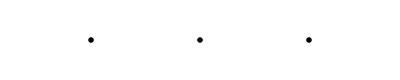

-Graphics-

-Graphics-

```mathematica
GraphicsRow[{ListPlot[Table[allCoeffListCheckFRFS[[i]][[2]],{i,Length[TList]}],Joined->True,PlotMarkers->{Automatic,8},ImageSize->100,PlotRange->{{Automatic,All},Automatic},AxesLabel->{"g","Tadpole to m23"}],ListPlot[Table[allCoeffListCheckFRFS[[i]][[3]],{i,Length[TList]}],Joined->True,PlotMarkers->{All,8},ImageSize->100,PlotRange->{{All,All},Automatic},AxesLabel->{"g","Tadpole to κ3"}],ListPlot[Table[allCoeffListCheckFRFS[[i]][[4]],{i,Length[TList]}],Joined->True,PlotMarkers->{All,8},ImageSize->100,PlotRange->{{All,All},Automatic},AxesLabel->{"g","Tadpole to λ3"}]},ImageSize->Full]
GraphicsRow[{ListPlot[Table[allCoeffListCheckFRFS[[i]][[5]],{i,Length[TList]}],Joined->True,PlotMarkers->{All,8},ImageSize->100,PlotRange->{{All,All},Automatic},AxesLabel->{"g","Tadpole to c51"}],ListPlot[Table[allCoeffListCheckFRFS[[i]][[6]],{i,Length[TList]}],Joined->True,PlotMarkers->{All,8},ImageSize->100,PlotRange->{{All,All},Automatic},AxesLabel->{"g","Tadpole to c61"}],ListPlot[Table[allCoeffListCheckFRFS[[i]][[7]],{i,Length[TList]}],Joined->True,PlotMarkers->{All,8},ImageSize->100,PlotRange->{{All,All},Automatic},AxesLabel->{"g","Tadpole to c71"}]},ImageSize->Full]
GraphicsRow[{ListPlot[Table[allCoeffListCheckFRFS[[i]][[8]],{i,Length[TList]}],Joined->True,PlotMarkers->{All,8},ImageSize->100,PlotRange->{{All,All},Automatic},AxesLabel->{"g","Tadpole to c81"}],ListPlot[Table[allCoeffListCheckFRFS[[i]][[9]],{i,Length[TList]}],Joined->True,PlotMarkers->{All,8},ImageSize->100,PlotRange->{{All,All},Automatic},AxesLabel->{"g","Tadpole to c82"}]},ImageSize->Full]
```

```mathematica
GraphicsRow[{ListPlot[Table[allCoeffListFRFS[[i]][[2]],{i,Length[TList]}],Joined->True,PlotMarkers->{Automatic,8},ImageSize->100,PlotRange->{{Automatic,All},Automatic},AxesLabel->{"g","FRFS m23"}],ListPlot[Table[allCoeffListFRFS[[i]][[3]],{i,Length[TList]}],Joined->True,PlotMarkers->{All,8},ImageSize->100,PlotRange->{{All,All},Automatic},AxesLabel->{"g","FRFS κ3"}],ListPlot[Table[allCoeffListFRFS[[i]][[4]],{i,Length[TList]}],Joined->True,PlotMarkers->{All,8},ImageSize->100,PlotRange->{{All,All},Automatic},AxesLabel->{"g","FRFS λ3"}]},ImageSize->Full]
GraphicsRow[{ListPlot[Table[allCoeffListFRFS[[i]][[5]],{i,Length[TList]}],Joined->True,PlotMarkers->{All,8},ImageSize->100,PlotRange->{{All,All},Automatic},AxesLabel->{"g","FRFS c51"}],ListPlot[Table[allCoeffListFRFS[[i]][[6]],{i,Length[TList]}],Joined->True,PlotMarkers->{All,8},ImageSize->100,PlotRange->{{All,All},Automatic},AxesLabel->{"g","FRFS c61"}],ListPlot[Table[allCoeffListFRFS[[i]][[7]],{i,Length[TList]}],Joined->True,PlotMarkers->{All,8},ImageSize->100,PlotRange->{{All,All},Automatic},AxesLabel->{"g","FRFS c71"}]},ImageSize->Full]
GraphicsRow[{ListPlot[Table[allCoeffListFRFS[[i]][[8]],{i,Length[TList]}],Joined->True,PlotMarkers->{All,8},ImageSize->100,PlotRange->{{All,All},Automatic},AxesLabel->{"g","FRFS c81"}],ListPlot[Table[allCoeffListFRFS[[i]][[9]],{i,Length[TList]}],Joined->True,PlotMarkers->{All,8},ImageSize->100,PlotRange->{{All,All},Automatic},AxesLabel->{"g","FRFS c82"}]},ImageSize->Full]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
GraphicsRow[{ListPlot[{allCoeffListFRF[[2]],allCoeffListFRFS[[2]]},Joined->True,PlotMarkers->{Automatic,8},ImageSize->100,PlotRange->{{Automatic,All},Automatic},AxesLabel->{"g","Relative m23"}],ListPlot[{allCoeffListFRF[[3]],allCoeffListFRFS[[3]]},Joined->True,PlotMarkers->{All,8},ImageSize->100,PlotRange->{{All,All},All},AxesLabel->{"g","Relative κ3"}],ListPlot[{allCoeffListFRF[[4]],allCoeffListFRFS[[4]]},Joined->True,PlotMarkers->{All,8},ImageSize->100,PlotRange->{{All,All},All},AxesLabel->{"g","Relative λ3"}]},ImageSize->Full]
GraphicsRow[{ListPlot[{allCoeffListFRF[[5]],allCoeffListFRFS[[5]]},Joined->True,PlotMarkers->{All,8},ImageSize->100,PlotRange->{{All,All},All},AxesLabel->{"g","Relative c51"}],ListPlot[{allCoeffListFRF[[6]],allCoeffListFRFS[[6]]},Joined->True,PlotMarkers->{All,8},ImageSize->100,PlotRange->{{All,All},All},AxesLabel->{"g","Relative c61"}],ListPlot[{allCoeffListFRF[[7]],allCoeffListFRFS[[7]]},Joined->True,PlotMarkers->{All,8},ImageSize->100,PlotRange->{{All,All},All},AxesLabel->{"g","Relative c71"}]},ImageSize->Full]
GraphicsRow[{ListPlot[{allCoeffListFRF[[8]],allCoeffListFRFS[[8]]},Joined->True,PlotMarkers->{All,8},ImageSize->100,PlotRange->{{All,All},All},AxesLabel->{"g","Relative c81"}],ListPlot[{allCoeffListFRF[[9]],allCoeffListFRFS[[9]]},Joined->True,PlotMarkers->{All,8},ImageSize->100,PlotRange->{{All,All},All},AxesLabel->{"g","Relative c82"}]},ImageSize->Full]
```

#### Compare matchings T

```mathematica
gList={0.8,1};

lastTadpole=0;
TList=Range[100, 500, 50];
relCoeffList=Table[{},{i,Length[gList]}];
allCoeffListFRFS=Table[{},{i,Length[gList]}];; allCoeffListFRF=Table[{},{i,Length[gList]}];; 
Do[
Do[
(* Load parameters for this iteration *)
{g0,T0}={gList[[t]],TList[[j]]};
SPTparameters={m2->m20, κ->κ0, λ->λ0,g->g0,T->T0};

{coeffListFRFS, coeffListFRF}=LoadOperators[];

relCoeffs=Table[{T0,Abs@(coeffListFRF[[k]]-coeffListFRFS[[k]])/Abs@coeffListFRFS[[k]]},{k,Length[coeffListFRF]}];
AppendTo[relCoeffList[[t]],relCoeffs];
AppendTo[allCoeffListFRFS[[t]],Table[{T0,coeffListFRFS[[k]]},{k,Length[coeffListFRFS]}]];
AppendTo[allCoeffListFRF[[t]],Table[{T0,coeffListFRF[[k]]},{k,Length[coeffListFRF]}]];
,
{j, Length[TList]}];

relCoeffList[[t]]=Transpose[relCoeffList[[t]]];
allCoeffListFRFS[[t]]=Transpose[allCoeffListFRFS[[t]]];
allCoeffListFRF[[t]]=Transpose[allCoeffListFRF[[t]]];


,{t,Length[gList]}]
```

```mathematica
relCoeffList[[1]]
```

```mathematica
(* Plot *)
GraphicsRow[{ListPlot[Table[relCoeffList[[i]][[2]],{i,Length[gList]}],Joined->True,PlotMarkers->{Automatic,8},ImageSize->100,PlotRange->{{Automatic,All},Automatic},AxesLabel->{"T","Relative m23"}],ListPlot[Table[relCoeffList[[i]][[3]],{i,Length[gList]}],Joined->True,PlotMarkers->{All,8},ImageSize->100,PlotRange->{{All,All},Automatic},AxesLabel->{"T","Relative κ3"}],ListPlot[Table[relCoeffList[[i]][[4]],{i,Length[gList]}],Joined->True,PlotMarkers->{All,8},ImageSize->100,PlotRange->{{All,All},Automatic},AxesLabel->{"T","Relative λ3"}]},ImageSize->Full]
GraphicsRow[{ListPlot[Table[relCoeffList[[i]][[5]],{i,Length[gList]}],Joined->True,PlotMarkers->{All,8},ImageSize->100,PlotRange->{{All,All},Automatic},AxesLabel->{"T","Relative c51"}],ListPlot[Table[relCoeffList[[i]][[6]],{i,Length[gList]}],Joined->True,PlotMarkers->{All,8},ImageSize->100,PlotRange->{{All,All},Automatic},AxesLabel->{"T","Relative c61"}],ListPlot[Table[relCoeffList[[i]][[7]],{i,Length[gList]}],Joined->True,PlotMarkers->{All,8},ImageSize->100,PlotRange->{{All,All},Automatic},AxesLabel->{"T","Relative c71"}]},ImageSize->Full]
GraphicsRow[{ListPlot[Table[relCoeffList[[i]][[8]],{i,Length[gList]}],Joined->True,PlotMarkers->{All,8},ImageSize->100,PlotRange->{{All,All},Automatic},AxesLabel->{"T","Relative c81"}],ListPlot[Table[relCoeffList[[i]][[9]],{i,Length[gList]}],Joined->True,PlotMarkers->{All,8},ImageSize->100,PlotRange->{{All,All},Automatic},AxesLabel->{"T","Relative c82"}]},ImageSize->Full]
```

```mathematica
GraphicsRow[{ListPlot[{allCoeffListFRF[[2]],allCoeffListFRFS[[2]]},Joined->True,PlotMarkers->{Automatic,8},ImageSize->100,PlotRange->{{Automatic,All},Automatic},AxesLabel->{"T","Relative m23"}],ListPlot[{allCoeffListFRF[[3]],allCoeffListFRFS[[3]]},Joined->True,PlotMarkers->{All,8},ImageSize->100,PlotRange->{{All,All},All},AxesLabel->{"T","Relative κ3"}],ListPlot[{allCoeffListFRF[[4]],allCoeffListFRFS[[4]]},Joined->True,PlotMarkers->{All,8},ImageSize->100,PlotRange->{{All,All},All},AxesLabel->{"T","Relative λ3"}]},ImageSize->Full]
GraphicsRow[{ListPlot[{allCoeffListFRF[[5]],allCoeffListFRFS[[5]]},Joined->True,PlotMarkers->{All,8},ImageSize->100,PlotRange->{{All,All},All},AxesLabel->{"T","Relative c51"}],ListPlot[{allCoeffListFRF[[6]],allCoeffListFRFS[[6]]},Joined->True,PlotMarkers->{All,8},ImageSize->100,PlotRange->{{All,All},All},AxesLabel->{"T","Relative c61"}],ListPlot[{allCoeffListFRF[[7]],allCoeffListFRFS[[7]]},Joined->True,PlotMarkers->{All,8},ImageSize->100,PlotRange->{{All,All},All},AxesLabel->{"T","Relative c71"}]},ImageSize->Full]
GraphicsRow[{ListPlot[{allCoeffListFRF[[8]],allCoeffListFRFS[[8]]},Joined->True,PlotMarkers->{All,8},ImageSize->100,PlotRange->{{All,All},All},AxesLabel->{"T","Relative c81"}],ListPlot[{allCoeffListFRF[[9]],allCoeffListFRFS[[9]]},Joined->True,PlotMarkers->{All,8},ImageSize->100,PlotRange->{{All,All},All},AxesLabel->{"T","Relative c82"}]},ImageSize->Full]
```